```mathematica
SetDirectory[NotebookDirectory[]];
```

E:\Google Drive\4A12\PenroseTilingThesis\Thesis\Figures

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

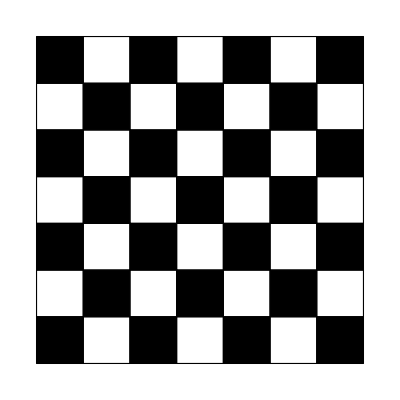

```mathematica
Graphics@{grid,blacks}
```

```mathematica
Export["Checkerboard.png",Graphics@{grid,blacks}]
```

Checkerboard.png

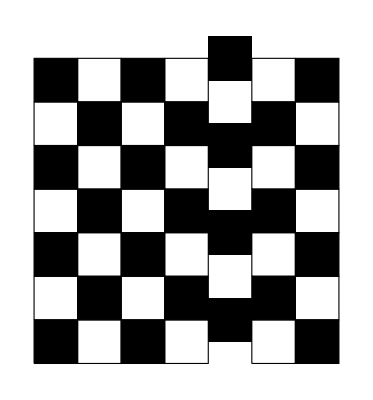

CheckerboardAperiodic.png

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%]
```

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

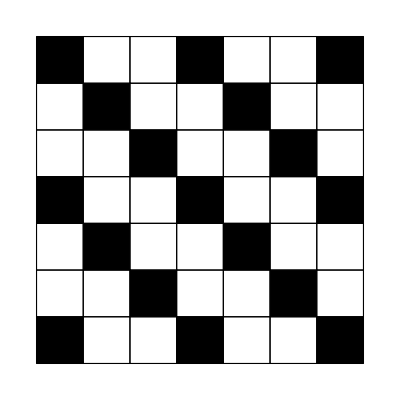

CheckerboardOther.png

```mathematica
Graphics@{grid,newblacks}
Export["CheckerboardOther.png",%]
```

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[Black],#}&/@circles],Pi/4];
Graphics[Rotate[circles,Pi/4]]
Table[Graphics[Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%]
```

-Graphics-

CheckerboardCircles.png

CheckerboardCircles.png